```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.29;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.913903},{0.01,-0.917799},{0.02,-0.921912},{0.03,-0.926234},{0.04,-0.930771},{0.05,-0.935523},{0.06,-0.940494},{0.07,-0.945686},{0.08,-0.951101},{0.09,-0.95674},{0.1,-0.962605},{0.11,-0.968707},{0.12,-0.975036},{0.13,-0.981609},{0.14,-0.988417},{0.15,-0.995477},{0.16,-1.00278},{0.17,-1.01034},{0.18,-1.01816},{0.19,-1.02623},{0.2,-1.03458},{0.21,-1.0432},{0.22,-1.0521},{0.23,-1.06128},{0.24,-1.07075},{0.25,-1.08054},{0.26,-1.09061},{0.27,-1.10098},{0.28,-1.1117},{0.29,-1.12274},{0.3,-1.1341},{0.31,-1.14581},{0.32,-1.15789},{0.33,-1.17032},{0.34,-1.18311},{0.35,-1.1963},{0.36,-1.20989},{0.37,-1.22389},{0.38,-1.23827},{0.39,-1.25311},{0.4,-1.26842},{0.41,-1.28417},{0.42,-1.30038},{0.43,-1.3171},{0.44,-1.33432},{0.45,-1.35206},{0.46,-1.37036},{0.47,-1.38921},{0.48,-1.40865},{0.49,-1.42869},{0.5,-1.44936},{0.51,-1.47069},{0.52,-1.49269},{0.53,-1.5154},{0.54,-1.53884},{0.55,-1.56305},{0.56,-1.58805},{0.57,-1.61388},{0.58,-1.64058},{0.59,-1.66818},{0.6,-1.69673},{0.61,-1.72626},{0.62,-1.75683},{0.63,-1.78847},{0.64,-1.82126},{0.65,-1.85523},{0.66,-1.89045},{0.67,-1.92699},{0.68,-1.9649},{0.69,-2.00427},{0.7,-2.04517},{0.71,-2.08769},{0.72,-2.13192},{0.73,-2.17795},{0.74,-2.22588},{0.75,-2.27585},{0.76,-2.32795},{0.77,-2.38234},{0.78,-2.43915},{0.79,-2.49854},{0.8,-2.56068},{0.81,-2.62576},{0.82,-2.69399},{0.83,-2.76557},{0.84,-2.84078},{0.85,-2.91985},{0.86,-3.00311},{0.87,-3.09088},{0.88,-3.18352},{0.89,-3.28145},{0.9,-3.38507},{0.91,-3.49497},{0.92,-3.61163},{0.93,-3.73577},{0.94,-3.86801},{0.95,-4.00927},{0.96,-4.16038},{0.97,-4.32249},{0.98,-4.49674},{0.99,-4.68457},{1.,-4.88761}}

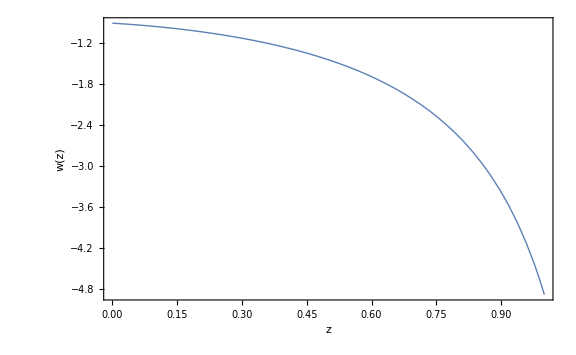

```mathematica
p04n=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.14637},{0.01,-1.1431},{0.02,-1.14005},{0.03,-1.13721},{0.04,-1.13458},{0.05,-1.13215},{0.06,-1.12992},{0.07,-1.12788},{0.08,-1.12604},{0.09,-1.12439},{0.1,-1.12292},{0.11,-1.12163},{0.12,-1.12052},{0.13,-1.11959},{0.14,-1.11883},{0.15,-1.11824},{0.16,-1.11782},{0.17,-1.11756},{0.18,-1.11746},{0.19,-1.11753},{0.2,-1.11775},{0.21,-1.11813},{0.22,-1.11866},{0.23,-1.11935},{0.24,-1.12018},{0.25,-1.12116},{0.26,-1.12229},{0.27,-1.12356},{0.28,-1.12498},{0.29,-1.12654},{0.3,-1.12823},{0.31,-1.13006},{0.32,-1.13204},{0.33,-1.13416},{0.34,-1.1364},{0.35,-1.13877},{0.36,-1.14129},{0.37,-1.14395},{0.38,-1.14672},{0.39,-1.14963},{0.4,-1.15267},{0.41,-1.15585},{0.42,-1.15915},{0.43,-1.16258},{0.44,-1.16613},{0.45,-1.16981},{0.46,-1.17363},{0.47,-1.17758},{0.48,-1.18165},{0.49,-1.18583},{0.5,-1.19016},{0.51,-1.19462},{0.52,-1.1992},{0.53,-1.2039},{0.54,-1.20873},{0.55,-1.21368},{0.56,-1.21878},{0.57,-1.224},{0.58,-1.22935},{0.59,-1.23482},{0.6,-1.24041},{0.61,-1.24614},{0.62,-1.25201},{0.63,-1.25801},{0.64,-1.26414},{0.65,-1.2704},{0.66,-1.27679},{0.67,-1.28331},{0.68,-1.28997},{0.69,-1.29677},{0.7,-1.3037},{0.71,-1.31077},{0.72,-1.31798},{0.73,-1.32533},{0.74,-1.33282},{0.75,-1.34046},{0.76,-1.34824},{0.77,-1.35616},{0.78,-1.36423},{0.79,-1.37244},{0.8,-1.38081},{0.81,-1.38933},{0.82,-1.398},{0.83,-1.40683},{0.84,-1.41581},{0.85,-1.42495},{0.86,-1.43425},{0.87,-1.44371},{0.88,-1.45334},{0.89,-1.46313},{0.9,-1.4731},{0.91,-1.48323},{0.92,-1.49354},{0.93,-1.50402},{0.94,-1.51468},{0.95,-1.52552},{0.96,-1.53655},{0.97,-1.54776},{0.98,-1.55917},{0.99,-1.57076},{1.,-1.58255}}

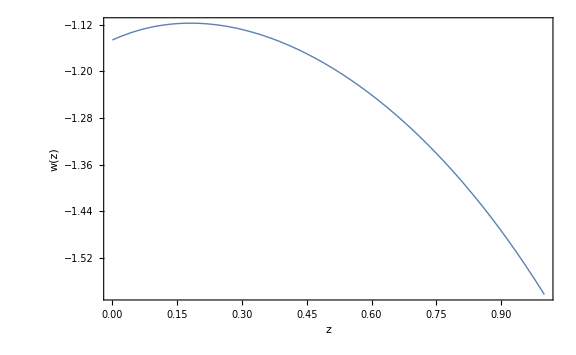

```mathematica
p02n=Plot[w[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.6113},{0.01,-1.58569},{0.02,-1.56094},{0.03,-1.537},{0.04,-1.51386},{0.05,-1.49146},{0.06,-1.46979},{0.07,-1.4488},{0.08,-1.42847},{0.09,-1.40877},{0.1,-1.38966},{0.11,-1.37114},{0.12,-1.35316},{0.13,-1.33571},{0.14,-1.31876},{0.15,-1.3023},{0.16,-1.2863},{0.17,-1.27074},{0.18,-1.25561},{0.19,-1.24087},{0.2,-1.22655},{0.21,-1.21258},{0.22,-1.19895},{0.23,-1.18568},{0.24,-1.17276},{0.25,-1.16015},{0.26,-1.14783},{0.27,-1.1358},{0.28,-1.12407},{0.29,-1.1126},{0.3,-1.10139},{0.31,-1.09043},{0.32,-1.07972},{0.33,-1.06923},{0.34,-1.05896},{0.35,-1.04892},{0.36,-1.03908},{0.37,-1.02944},{0.38,-1.01999},{0.39,-1.01074},{0.4,-1.00165},{0.41,-0.992746},{0.42,-0.984015},{0.43,-0.975439},{0.44,-0.967016},{0.45,-0.95875},{0.46,-0.950638},{0.47,-0.94266},{0.48,-0.934817},{0.49,-0.92711},{0.5,-0.919542},{0.51,-0.912092},{0.52,-0.904758},{0.53,-0.897543},{0.54,-0.890452},{0.55,-0.883474},{0.56,-0.876593},{0.57,-0.869813},{0.58,-0.863137},{0.59,-0.856569},{0.6,-0.850104},{0.61,-0.84372},{0.62,-0.837421},{0.63,-0.831211},{0.64,-0.825093},{0.65,-0.819071},{0.66,-0.813126},{0.67,-0.807249},{0.68,-0.801446},{0.69,-0.79572},{0.7,-0.790075},{0.71,-0.784515},{0.72,-0.779019},{0.73,-0.77358},{0.74,-0.768203},{0.75,-0.762891},{0.76,-0.757649},{0.77,-0.75248},{0.78,-0.747379},{0.79,-0.742323},{0.8,-0.737317},{0.81,-0.732363},{0.82,-0.727468},{0.83,-0.722634},{0.84,-0.717866},{0.85,-0.713156},{0.86,-0.708481},{0.87,-0.703847},{0.88,-0.699257},{0.89,-0.694716},{0.9,-0.690228},{0.91,-0.685797},{0.92,-0.681418},{0.93,-0.677069},{0.94,-0.672761},{0.95,-0.668496},{0.96,-0.664279},{0.97,-0.6601},{0.98,-0.655956},{0.99,-0.651852},{1.,-0.647793}}

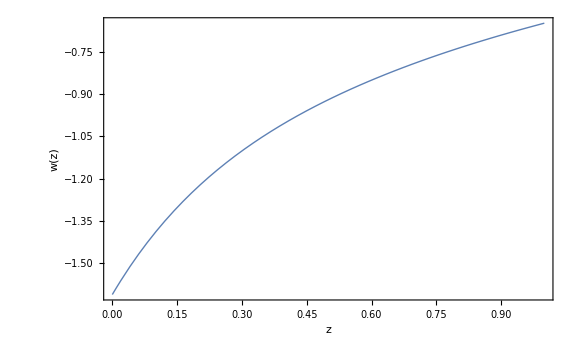

```mathematica
p02=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.84376},{0.01,-1.80306},{0.02,-1.76401},{0.03,-1.72652},{0.04,-1.69051},{0.05,-1.6559},{0.06,-1.62262},{0.07,-1.59057},{0.08,-1.55972},{0.09,-1.52999},{0.1,-1.50132},{0.11,-1.47366},{0.12,-1.44696},{0.13,-1.42116},{0.14,-1.39623},{0.15,-1.3721},{0.16,-1.34877},{0.17,-1.32616},{0.18,-1.30426},{0.19,-1.28303},{0.2,-1.26243},{0.21,-1.24245},{0.22,-1.22304},{0.23,-1.20419},{0.24,-1.18586},{0.25,-1.16804},{0.26,-1.1507},{0.27,-1.13382},{0.28,-1.11738},{0.29,-1.10137},{0.3,-1.08575},{0.31,-1.07055},{0.32,-1.05572},{0.33,-1.04121},{0.34,-1.02704},{0.35,-1.0132},{0.36,-0.999703},{0.37,-0.986539},{0.38,-0.973645},{0.39,-0.961013},{0.4,-0.94865},{0.41,-0.93656},{0.42,-0.924747},{0.43,-0.913173},{0.44,-0.901811},{0.45,-0.89067},{0.46,-0.879754},{0.47,-0.869069},{0.48,-0.8586},{0.49,-0.84831},{0.5,-0.838204},{0.51,-0.828289},{0.52,-0.818571},{0.53,-0.809025},{0.54,-0.799633},{0.55,-0.790402},{0.56,-0.781339},{0.57,-0.772449},{0.58,-0.763698},{0.59,-0.75508},{0.6,-0.746601},{0.61,-0.738268},{0.62,-0.730088},{0.63,-0.722032},{0.64,-0.714086},{0.65,-0.706258},{0.66,-0.698555},{0.67,-0.690985},{0.68,-0.683536},{0.69,-0.676181},{0.7,-0.668927},{0.71,-0.661783},{0.72,-0.654757},{0.73,-0.647831},{0.74,-0.640988},{0.75,-0.634236},{0.76,-0.627584},{0.77,-0.621038},{0.78,-0.614581},{0.79,-0.608195},{0.8,-0.601888},{0.81,-0.59567},{0.82,-0.589546},{0.83,-0.583511},{0.84,-0.577536},{0.85,-0.571628},{0.86,-0.565795},{0.87,-0.560044},{0.88,-0.554383},{0.89,-0.548784},{0.9,-0.543238},{0.91,-0.537752},{0.92,-0.532335},{0.93,-0.526995},{0.94,-0.521732},{0.95,-0.516519},{0.96,-0.511355},{0.97,-0.506249},{0.98,-0.501209},{0.99,-0.496236},{1.,-0.49131}}

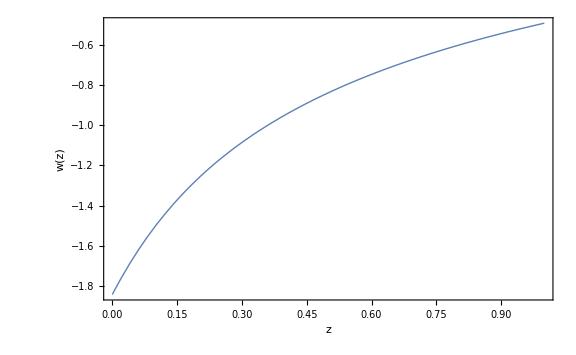

```mathematica
p04=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

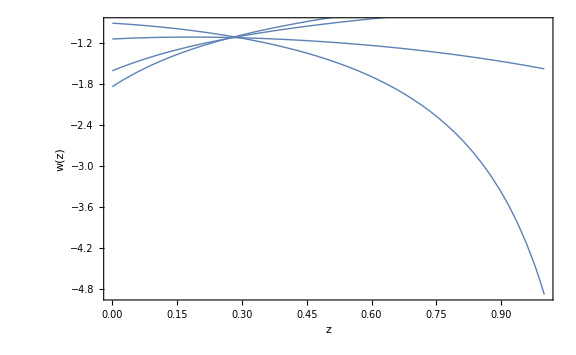

```mathematica
Show[p04n, p02n, p02, p04]
```

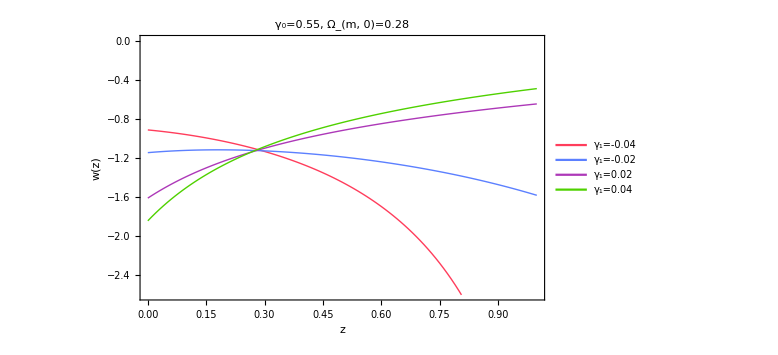

```mathematica
list2=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Thick, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.28", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points11=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.913903},{0.01,-0.917799},{0.02,-0.921912},{0.03,-0.926234},{0.04,-0.930771},{0.05,-0.935523},{0.06,-0.940494},{0.07,-0.945686},{0.08,-0.951101},{0.09,-0.95674},{0.1,-0.962605},{0.11,-0.968707},{0.12,-0.975036},{0.13,-0.981609},{0.14,-0.988417},{0.15,-0.995477},{0.16,-1.00278},{0.17,-1.01034},{0.18,-1.01816},{0.19,-1.02623},{0.2,-1.03458},{0.21,-1.0432},{0.22,-1.0521},{0.23,-1.06128},{0.24,-1.07075},{0.25,-1.08054},{0.26,-1.09061},{0.27,-1.10098},{0.28,-1.1117},{0.29,-1.12274},{0.3,-1.1341},{0.31,-1.14581},{0.32,-1.15789},{0.33,-1.17032},{0.34,-1.18311},{0.35,-1.1963},{0.36,-1.20989},{0.37,-1.22389},{0.38,-1.23827},{0.39,-1.25311},{0.4,-1.26842},{0.41,-1.28417},{0.42,-1.30038},{0.43,-1.3171},{0.44,-1.33432},{0.45,-1.35206},{0.46,-1.37036},{0.47,-1.38921},{0.48,-1.40865},{0.49,-1.42869},{0.5,-1.44936},{0.51,-1.47069},{0.52,-1.49269},{0.53,-1.5154},{0.54,-1.53884},{0.55,-1.56305},{0.56,-1.58805},{0.57,-1.61388},{0.58,-1.64058},{0.59,-1.66818},{0.6,-1.69673},{0.61,-1.72626},{0.62,-1.75683},{0.63,-1.78847},{0.64,-1.82126},{0.65,-1.85523},{0.66,-1.89045},{0.67,-1.92699},{0.68,-1.9649},{0.69,-2.00427},{0.7,-2.04517},{0.71,-2.08769},{0.72,-2.13192},{0.73,-2.17795},{0.74,-2.22588},{0.75,-2.27585},{0.76,-2.32795},{0.77,-2.38234},{0.78,-2.43915},{0.79,-2.49854},{0.8,-2.56068},{0.81,-2.62576},{0.82,-2.69399},{0.83,-2.76557},{0.84,-2.84078},{0.85,-2.91985},{0.86,-3.00311},{0.87,-3.09088},{0.88,-3.18352},{0.89,-3.28145},{0.9,-3.38507},{0.91,-3.49497},{0.92,-3.61163},{0.93,-3.73577},{0.94,-3.86801},{0.95,-4.00927},{0.96,-4.16038},{0.97,-4.32249},{0.98,-4.49674},{0.99,-4.68457},{1.,-4.88761}}

```mathematica
p04n=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points22=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.13412},{0.01,-1.13104},{0.02,-1.12818},{0.03,-1.12552},{0.04,-1.12307},{0.05,-1.12082},{0.06,-1.11877},{0.07,-1.11691},{0.08,-1.11524},{0.09,-1.11375},{0.1,-1.11245},{0.11,-1.11132},{0.12,-1.11038},{0.13,-1.1096},{0.14,-1.109},{0.15,-1.10856},{0.16,-1.10829},{0.17,-1.10818},{0.18,-1.10823},{0.19,-1.10844},{0.2,-1.1088},{0.21,-1.10932},{0.22,-1.10999},{0.23,-1.11081},{0.24,-1.11178},{0.25,-1.11288},{0.26,-1.11414},{0.27,-1.11554},{0.28,-1.11708},{0.29,-1.11876},{0.3,-1.12058},{0.31,-1.12253},{0.32,-1.12462},{0.33,-1.12685},{0.34,-1.12921},{0.35,-1.1317},{0.36,-1.13431},{0.37,-1.13707},{0.38,-1.13996},{0.39,-1.14298},{0.4,-1.14611},{0.41,-1.14938},{0.42,-1.15279},{0.43,-1.15632},{0.44,-1.15997},{0.45,-1.16374},{0.46,-1.16765},{0.47,-1.17169},{0.48,-1.17586},{0.49,-1.18014},{0.5,-1.18454},{0.51,-1.18908},{0.52,-1.19374},{0.53,-1.19854},{0.54,-1.20346},{0.55,-1.20849},{0.56,-1.21365},{0.57,-1.21895},{0.58,-1.22438},{0.59,-1.22993},{0.6,-1.23561},{0.61,-1.24141},{0.62,-1.24734},{0.63,-1.25341},{0.64,-1.25961},{0.65,-1.26595},{0.66,-1.27241},{0.67,-1.279},{0.68,-1.28572},{0.69,-1.29259},{0.7,-1.29959},{0.71,-1.30672},{0.72,-1.31399},{0.73,-1.32141},{0.74,-1.32896},{0.75,-1.33665},{0.76,-1.34449},{0.77,-1.35247},{0.78,-1.3606},{0.79,-1.36887},{0.8,-1.37729},{0.81,-1.38587},{0.82,-1.3946},{0.83,-1.40348},{0.84,-1.41251},{0.85,-1.4217},{0.86,-1.43106},{0.87,-1.44057},{0.88,-1.45025},{0.89,-1.46009},{0.9,-1.4701},{0.91,-1.48029},{0.92,-1.49064},{0.93,-1.50117},{0.94,-1.51188},{0.95,-1.52277},{0.96,-1.53384},{0.97,-1.5451},{0.98,-1.55655},{0.99,-1.56818},{1.,-1.58002}}

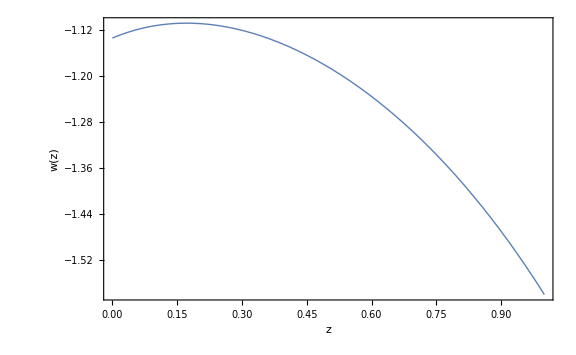

```mathematica
p02n=Plot[w[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points33=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.59278},{0.01,-1.56769},{0.02,-1.54344},{0.03,-1.52},{0.04,-1.49732},{0.05,-1.47539},{0.06,-1.45415},{0.07,-1.4336},{0.08,-1.41367},{0.09,-1.39437},{0.1,-1.37565},{0.11,-1.3575},{0.12,-1.33988},{0.13,-1.32278},{0.14,-1.30617},{0.15,-1.29003},{0.16,-1.27434},{0.17,-1.25908},{0.18,-1.24424},{0.19,-1.22979},{0.2,-1.21573},{0.21,-1.20202},{0.22,-1.18866},{0.23,-1.17563},{0.24,-1.16295},{0.25,-1.15056},{0.26,-1.13846},{0.27,-1.12665},{0.28,-1.11513},{0.29,-1.10386},{0.3,-1.09284},{0.31,-1.08206},{0.32,-1.07154},{0.33,-1.06122},{0.34,-1.05113},{0.35,-1.04124},{0.36,-1.03157},{0.37,-1.02209},{0.38,-1.01278},{0.39,-1.00367},{0.4,-0.994734},{0.41,-0.985972},{0.42,-0.977362},{0.43,-0.968909},{0.44,-0.960615},{0.45,-0.95248},{0.46,-0.944482},{0.47,-0.936614},{0.48,-0.928879},{0.49,-0.92128},{0.5,-0.91382},{0.51,-0.906475},{0.52,-0.89924},{0.53,-0.892117},{0.54,-0.88511},{0.55,-0.878222},{0.56,-0.871444},{0.57,-0.864755},{0.58,-0.85816},{0.59,-0.851661},{0.6,-0.845262},{0.61,-0.838967},{0.62,-0.832756},{0.63,-0.826623},{0.64,-0.82057},{0.65,-0.814603},{0.66,-0.808725},{0.67,-0.802927},{0.68,-0.797194},{0.69,-0.791531},{0.7,-0.785941},{0.71,-0.780429},{0.72,-0.774996},{0.73,-0.76962},{0.74,-0.764301},{0.75,-0.759045},{0.76,-0.753854},{0.77,-0.748733},{0.78,-0.74368},{0.79,-0.738673},{0.8,-0.733716},{0.81,-0.728812},{0.82,-0.723965},{0.83,-0.719181},{0.84,-0.714457},{0.85,-0.709775},{0.86,-0.705135},{0.87,-0.700543},{0.88,-0.696003},{0.89,-0.691519},{0.9,-0.68708},{0.91,-0.682678},{0.92,-0.678317},{0.93,-0.674},{0.94,-0.669733},{0.95,-0.665514},{0.96,-0.661327},{0.97,-0.657175},{0.98,-0.653061},{0.99,-0.64899},{1.,-0.644966}}

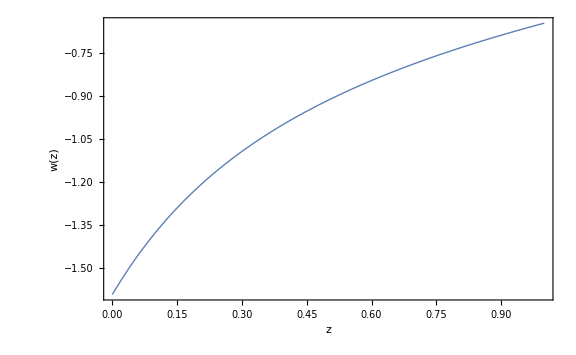

```mathematica
p02=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points44=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.82211},{0.01,-1.78217},{0.02,-1.74385},{0.03,-1.70707},{0.04,-1.67173},{0.05,-1.63776},{0.06,-1.60509},{0.07,-1.57363},{0.08,-1.54334},{0.09,-1.51415},{0.1,-1.48599},{0.11,-1.45882},{0.12,-1.43259},{0.13,-1.40724},{0.14,-1.38274},{0.15,-1.35902},{0.16,-1.33608},{0.17,-1.31384},{0.18,-1.29231},{0.19,-1.27142},{0.2,-1.25115},{0.21,-1.23149},{0.22,-1.21238},{0.23,-1.19382},{0.24,-1.17577},{0.25,-1.15821},{0.26,-1.14114},{0.27,-1.1245},{0.28,-1.1083},{0.29,-1.09252},{0.3,-1.07712},{0.31,-1.06211},{0.32,-1.04749},{0.33,-1.0332},{0.34,-1.01922},{0.35,-1.00555},{0.36,-0.992206},{0.37,-0.979188},{0.38,-0.966481},{0.39,-0.95402},{0.4,-0.94181},{0.41,-0.929856},{0.42,-0.918163},{0.43,-0.906732},{0.44,-0.895516},{0.45,-0.884505},{0.46,-0.873706},{0.47,-0.863125},{0.48,-0.852766},{0.49,-0.842599},{0.5,-0.832604},{0.51,-0.822788},{0.52,-0.813158},{0.53,-0.803715},{0.54,-0.794425},{0.55,-0.785285},{0.56,-0.776305},{0.57,-0.76749},{0.58,-0.758832},{0.59,-0.750299},{0.6,-0.741898},{0.61,-0.733637},{0.62,-0.725521},{0.63,-0.717543},{0.64,-0.709672},{0.65,-0.701913},{0.66,-0.694273},{0.67,-0.68676},{0.68,-0.679375},{0.69,-0.672084},{0.7,-0.66489},{0.71,-0.657801},{0.72,-0.650825},{0.73,-0.643957},{0.74,-0.63717},{0.75,-0.63047},{0.76,-0.623865},{0.77,-0.617363},{0.78,-0.610957},{0.79,-0.60462},{0.8,-0.59836},{0.81,-0.592183},{0.82,-0.586098},{0.83,-0.580106},{0.84,-0.574175},{0.85,-0.568308},{0.86,-0.562513},{0.87,-0.556798},{0.88,-0.551169},{0.89,-0.545611},{0.9,-0.540103},{0.91,-0.534653},{0.92,-0.529269},{0.93,-0.523959},{0.94,-0.518728},{0.95,-0.513548},{0.96,-0.508416},{0.97,-0.50334},{0.98,-0.498328},{0.99,-0.493384},{1.,-0.488487}}

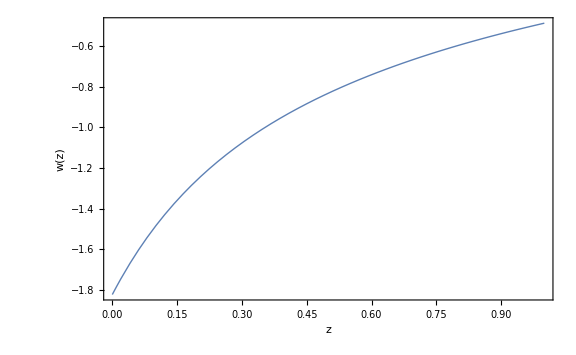

```mathematica
p04=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

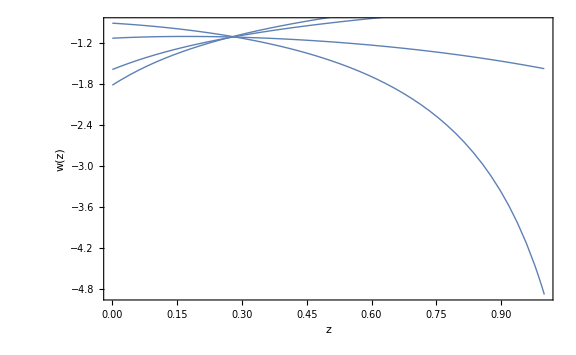

```mathematica
Show[p04n, p02n, p02, p04]
```

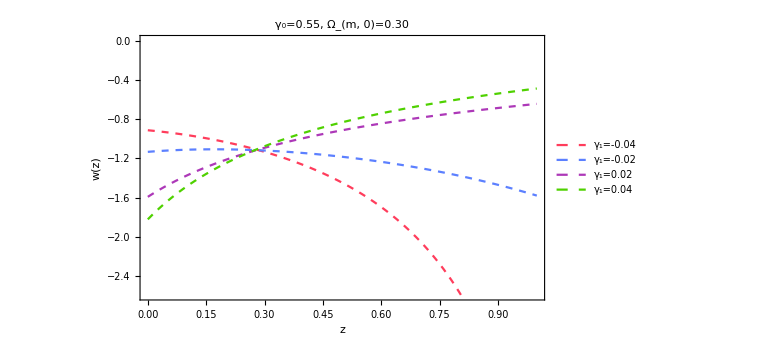

```mathematica
list3=ListLinePlot[{points11,points22,points33, points44}, PlotStyle->{{Dashed, RGBColor[1,0.24,0.36]}, {Dashed, RGBColor[0.36,0.5,1]}, {Dashed, RGBColor[0.68,0.22,0.72]}, {Dashed, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.30", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.31;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points111=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.904793},{0.01,-0.908795},{0.02,-0.913012},{0.03,-0.917438},{0.04,-0.922077},{0.05,-0.92693},{0.06,-0.932001},{0.07,-0.93729},{0.08,-0.942802},{0.09,-0.948537},{0.1,-0.954497},{0.11,-0.960693},{0.12,-0.967113},{0.13,-0.973778},{0.14,-0.980676},{0.15,-0.987825},{0.16,-0.995215},{0.17,-1.00286},{0.18,-1.01076},{0.19,-1.01893},{0.2,-1.02736},{0.21,-1.03606},{0.22,-1.04505},{0.23,-1.0543},{0.24,-1.06386},{0.25,-1.07373},{0.26,-1.08387},{0.27,-1.09433},{0.28,-1.10513},{0.29,-1.11624},{0.3,-1.12767},{0.31,-1.13946},{0.32,-1.15162},{0.33,-1.16412},{0.34,-1.17698},{0.35,-1.19024},{0.36,-1.20391},{0.37,-1.21798},{0.38,-1.23243},{0.39,-1.24735},{0.4,-1.26272},{0.41,-1.27854},{0.42,-1.29482},{0.43,-1.31161},{0.44,-1.3289},{0.45,-1.34671},{0.46,-1.36507},{0.47,-1.38399},{0.48,-1.4035},{0.49,-1.42361},{0.5,-1.44434},{0.51,-1.46574},{0.52,-1.4878},{0.53,-1.51058},{0.54,-1.53408},{0.55,-1.55836},{0.56,-1.58342},{0.57,-1.60932},{0.58,-1.63608},{0.59,-1.66374},{0.6,-1.69235},{0.61,-1.72195},{0.62,-1.75258},{0.63,-1.78429},{0.64,-1.81713},{0.65,-1.85117},{0.66,-1.88645},{0.67,-1.92305},{0.68,-1.96103},{0.69,-2.00046},{0.7,-2.04143},{0.71,-2.084},{0.72,-2.12829},{0.73,-2.17438},{0.74,-2.22238},{0.75,-2.27241},{0.76,-2.32458},{0.77,-2.37903},{0.78,-2.4359},{0.79,-2.49535},{0.8,-2.55755},{0.81,-2.6227},{0.82,-2.69099},{0.83,-2.76263},{0.84,-2.8379},{0.85,-2.91704},{0.86,-3.00037},{0.87,-3.0882},{0.88,-3.1809},{0.89,-3.27889},{0.9,-3.38258},{0.91,-3.49255},{0.92,-3.60927},{0.93,-3.73347},{0.94,-3.86578},{0.95,-4.0071},{0.96,-4.15828},{0.97,-4.32045},{0.98,-4.49476},{0.99,-4.68266},{1.,-4.88576}}

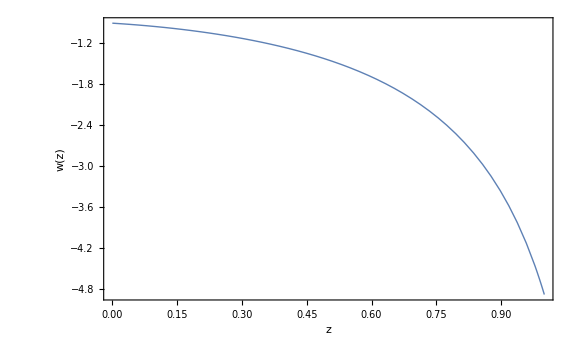

```mathematica
p04n=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points222=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.12225},{0.01,-1.11936},{0.02,-1.11668},{0.03,-1.11421},{0.04,-1.11194},{0.05,-1.10986},{0.06,-1.10798},{0.07,-1.10629},{0.08,-1.10478},{0.09,-1.10346},{0.1,-1.10232},{0.11,-1.10136},{0.12,-1.10057},{0.13,-1.09995},{0.14,-1.0995},{0.15,-1.09921},{0.16,-1.09908},{0.17,-1.09912},{0.18,-1.09932},{0.19,-1.09966},{0.2,-1.10016},{0.21,-1.10082},{0.22,-1.10162},{0.23,-1.10257},{0.24,-1.10366},{0.25,-1.1049},{0.26,-1.10628},{0.27,-1.1078},{0.28,-1.10946},{0.29,-1.11126},{0.3,-1.11319},{0.31,-1.11526},{0.32,-1.11746},{0.33,-1.1198},{0.34,-1.12227},{0.35,-1.12487},{0.36,-1.12759},{0.37,-1.13045},{0.38,-1.13345},{0.39,-1.13656},{0.4,-1.13979},{0.41,-1.14316},{0.42,-1.14667},{0.43,-1.15029},{0.44,-1.15403},{0.45,-1.1579},{0.46,-1.1619},{0.47,-1.16603},{0.48,-1.17028},{0.49,-1.17464},{0.5,-1.17913},{0.51,-1.18375},{0.52,-1.1885},{0.53,-1.19338},{0.54,-1.19837},{0.55,-1.20348},{0.56,-1.20872},{0.57,-1.2141},{0.58,-1.2196},{0.59,-1.22523},{0.6,-1.23098},{0.61,-1.23685},{0.62,-1.24285},{0.63,-1.24899},{0.64,-1.25526},{0.65,-1.26167},{0.66,-1.2682},{0.67,-1.27485},{0.68,-1.28164},{0.69,-1.28856},{0.7,-1.29563},{0.71,-1.30282},{0.72,-1.31016},{0.73,-1.31763},{0.74,-1.32524},{0.75,-1.33299},{0.76,-1.34089},{0.77,-1.34893},{0.78,-1.35711},{0.79,-1.36544},{0.8,-1.37392},{0.81,-1.38254},{0.82,-1.39132},{0.83,-1.40025},{0.84,-1.40934},{0.85,-1.41859},{0.86,-1.42799},{0.87,-1.43755},{0.88,-1.44728},{0.89,-1.45717},{0.9,-1.46723},{0.91,-1.47746},{0.92,-1.48786},{0.93,-1.49844},{0.94,-1.50919},{0.95,-1.52012},{0.96,-1.53124},{0.97,-1.54254},{0.98,-1.55403},{0.99,-1.56571},{1.,-1.57758}}

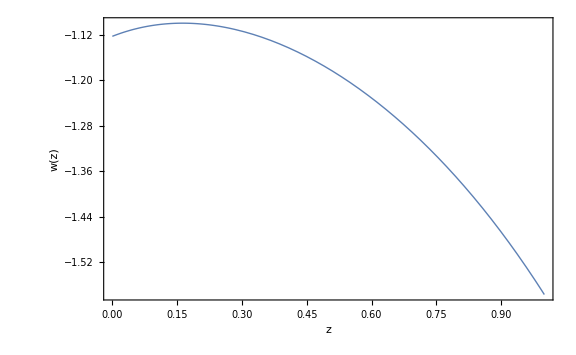

```mathematica
p02n=Plot[w[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points333=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.57488},{0.01,-1.5503},{0.02,-1.52655},{0.03,-1.50358},{0.04,-1.48136},{0.05,-1.45987},{0.06,-1.43907},{0.07,-1.41892},{0.08,-1.3994},{0.09,-1.38049},{0.1,-1.36214},{0.11,-1.34435},{0.12,-1.32708},{0.13,-1.31031},{0.14,-1.29402},{0.15,-1.2782},{0.16,-1.26281},{0.17,-1.24784},{0.18,-1.23328},{0.19,-1.2191},{0.2,-1.2053},{0.21,-1.19186},{0.22,-1.17874},{0.23,-1.16595},{0.24,-1.15349},{0.25,-1.14132},{0.26,-1.12944},{0.27,-1.11784},{0.28,-1.10651},{0.29,-1.09544},{0.3,-1.0846},{0.31,-1.07401},{0.32,-1.06366},{0.33,-1.05351},{0.34,-1.04358},{0.35,-1.03385},{0.36,-1.02434},{0.37,-1.015},{0.38,-1.00584},{0.39,-0.996864},{0.4,-0.988066},{0.41,-0.979436},{0.42,-0.970955},{0.43,-0.962626},{0.44,-0.95445},{0.45,-0.946431},{0.46,-0.938547},{0.47,-0.930789},{0.48,-0.923161},{0.49,-0.915665},{0.5,-0.908305},{0.51,-0.901059},{0.52,-0.893919},{0.53,-0.886888},{0.54,-0.879971},{0.55,-0.873169},{0.56,-0.866477},{0.57,-0.859871},{0.58,-0.853356},{0.59,-0.846936},{0.6,-0.840613},{0.61,-0.834391},{0.62,-0.828254},{0.63,-0.822191},{0.64,-0.816207},{0.65,-0.810306},{0.66,-0.804493},{0.67,-0.798759},{0.68,-0.793088},{0.69,-0.787485},{0.7,-0.781955},{0.71,-0.7765},{0.72,-0.771122},{0.73,-0.765802},{0.74,-0.760537},{0.75,-0.755332},{0.76,-0.750192},{0.77,-0.745121},{0.78,-0.740116},{0.79,-0.735157},{0.8,-0.730246},{0.81,-0.725387},{0.82,-0.720586},{0.83,-0.715845},{0.84,-0.711163},{0.85,-0.706522},{0.86,-0.701923},{0.87,-0.697371},{0.88,-0.692869},{0.89,-0.688423},{0.9,-0.684022},{0.91,-0.679656},{0.92,-0.67533},{0.93,-0.671048},{0.94,-0.666815},{0.95,-0.66263},{0.96,-0.658475},{0.97,-0.654355},{0.98,-0.650272},{0.99,-0.646232},{1.,-0.642238}}

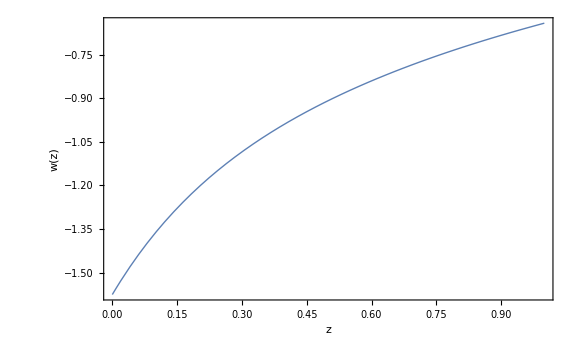

```mathematica
p02=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points444=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.8012},{0.01,-1.76201},{0.02,-1.7244},{0.03,-1.6883},{0.04,-1.65361},{0.05,-1.62027},{0.06,-1.58819},{0.07,-1.5573},{0.08,-1.52756},{0.09,-1.49888},{0.1,-1.47122},{0.11,-1.44452},{0.12,-1.41874},{0.13,-1.39382},{0.14,-1.36974},{0.15,-1.34641},{0.16,-1.32385},{0.17,-1.30198},{0.18,-1.28079},{0.19,-1.26024},{0.2,-1.24028},{0.21,-1.22093},{0.22,-1.20211},{0.23,-1.18382},{0.24,-1.16605},{0.25,-1.14875},{0.26,-1.13192},{0.27,-1.11552},{0.28,-1.09954},{0.29,-1.08398},{0.3,-1.0688},{0.31,-1.05399},{0.32,-1.03955},{0.33,-1.02545},{0.34,-1.01166},{0.35,-0.998174},{0.36,-0.985005},{0.37,-0.972155},{0.38,-0.959585},{0.39,-0.947263},{0.4,-0.935197},{0.41,-0.923391},{0.42,-0.911849},{0.43,-0.900536},{0.44,-0.88943},{0.45,-0.878538},{0.46,-0.867866},{0.47,-0.85742},{0.48,-0.847164},{0.49,-0.837084},{0.5,-0.827188},{0.51,-0.817483},{0.52,-0.807964},{0.53,-0.798598},{0.54,-0.789387},{0.55,-0.780338},{0.56,-0.771459},{0.57,-0.762733},{0.58,-0.754134},{0.59,-0.745671},{0.6,-0.73735},{0.61,-0.729179},{0.62,-0.721142},{0.63,-0.713211},{0.64,-0.705397},{0.65,-0.697705},{0.66,-0.690144},{0.67,-0.682706},{0.68,-0.675363},{0.69,-0.668119},{0.7,-0.660984},{0.71,-0.653965},{0.72,-0.647049},{0.73,-0.640214},{0.74,-0.633471},{0.75,-0.626825},{0.76,-0.620286},{0.77,-0.613835},{0.78,-0.607455},{0.79,-0.601154},{0.8,-0.594942},{0.81,-0.588823},{0.82,-0.582792},{0.83,-0.576821},{0.84,-0.570916},{0.85,-0.565087},{0.86,-0.559341},{0.87,-0.553684},{0.88,-0.548087},{0.89,-0.542542},{0.9,-0.537059},{0.91,-0.531645},{0.92,-0.526308},{0.93,-0.521044},{0.94,-0.515827},{0.95,-0.510667},{0.96,-0.505572},{0.97,-0.500539},{0.98,-0.495555},{0.99,-0.490626},{1.,-0.48576}}

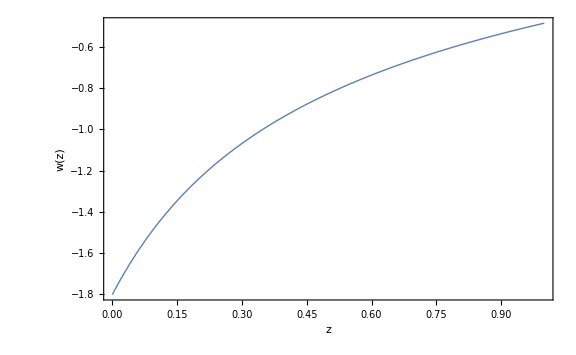

```mathematica
p04=Plot[w[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

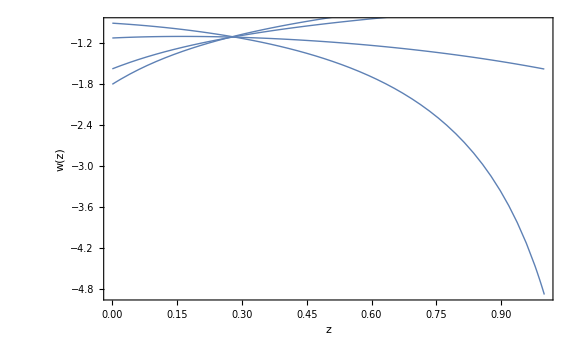

```mathematica
Show[p04n, p02n, p02, p04]
```

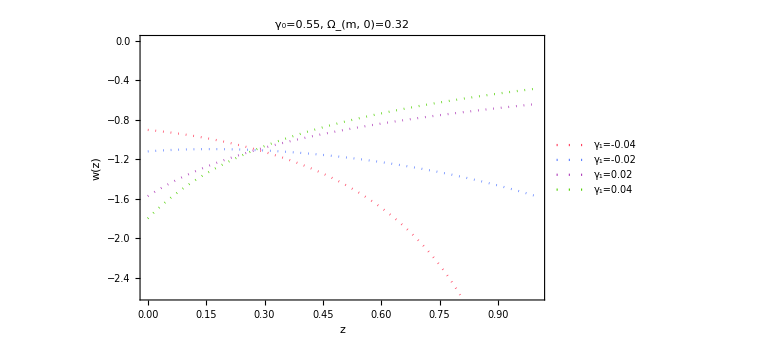

```mathematica
list4=ListLinePlot[{points111,points222,points333, points444}, PlotStyle->{{Dotted, RGBColor[1,0.24,0.36]}, {Dotted, RGBColor[0.36,0.5,1]}, {Dotted, RGBColor[0.68,0.22,0.72]}, {Dotted, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.32", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

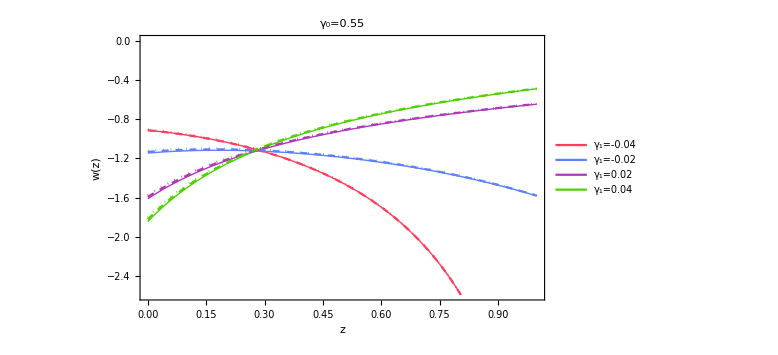

```mathematica
list5=ListLinePlot[{points1,points2,points3, points4, points11,points22,points33, points44, points111,points222,points333, points444}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Thick, RGBColor[0.31,0.82,0]}, {Dashed, RGBColor[1,0.24,0.36]}, {Dashed, RGBColor[0.36,0.5,1]}, {Dashed, RGBColor[0.68,0.22,0.72]}, {Dashed, RGBColor[0.31,0.82,0]},{Dotted, RGBColor[1,0.24,0.36]}, {Dotted, RGBColor[0.36,0.5,1]}, {Dotted, RGBColor[0.68,0.22,0.72]}, {Dotted, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
SetDirectory["G:\\My Drive\\U\\paper"]
```

G:\My Drive\U\paper

```mathematica
Export["w(z)_om029.pdf",list2,ImageResolution->500]
```

w(z)_om029.pdf

```mathematica
Export["w(z)_om030.pdf",list3,ImageResolution->500]
```

w(z)_om030.pdf

```mathematica
Export["w(z)_om031.pdf",list4,ImageResolution->500]
```

w(z)_om031.pdf

```mathematica
Export["w(z)_all_2931.pdf",list5,ImageResolution->500]
```

w(z)_all_2931.pdf